```mathematica
train1 = {1400-> 225000, 1900 -> 235000, 980 -> 140000, 2300 -> 350000}
```

{1400→225000,1900→235000,980→140000,2300→350000}

```mathematica
test1 = {1800->240000, 2000->215000, 2200->375000}
```

{1800→240000,2000→215000,2200→375000}

```mathematica
pmodel = Predict[train1]
```

PredictorFunction[…]

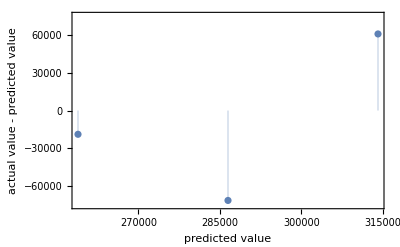

```mathematica
PredictorMeasurements[pmodel, test1, "ResidualPlot"]
```

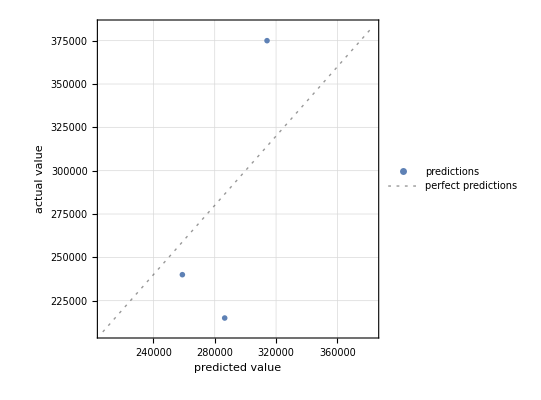

```mathematica
PredictorMeasurements[pmodel, test1, "ComparisonPlot"]
```